```mathematica
G=1;
cs=1;
M = 1;
rho0 = 1;
ϕ[ξ_,e_]:=2 ArcTan[Sqrt[(1+e)/(1-e)] Tan[ξ/2]];

(*(factorial(ℓ-m)/factorial(ℓ+m))*(Plm(0,ℓ,m))^2*)
plmfact[ℓ_,m_]:=If[OddQ[ℓ+m],0,Module[{factor=1.0,k},Do[factor/=k;
If[OddQ[k],factor*=k^2],{k,1,ℓ+m}];
Do[factor*=k;
If[EvenQ[k],factor/=k^2],{k,1,ℓ-m}];
factor]]

(*clm factor*)
cℓm[ℓ_,m_]:=(2 ℓ+1) plmfact[ℓ,m]

trueAnomaly[ξ_,e_]:=2 ArcTan[Sqrt[(1+e)/(1-e)] Tan[ξ/2]]

sphericalBesselJ[ν_,x_]:=Sign[x]^ν BesselJ[ν+1/2,Abs[x]]/Sqrt[2 Abs[x]/π]

(*The gjlm function computed by numerical integration*)
g1[j_,l_,m_,x_,e_]:=NIntegrate[(1-e Cos[ξ]) SphericalBesselJ[l,x (1-e Cos[ξ])] Cos[(m ϕ[ξ,e]-j (ξ-e Sin[ξ]))]/(2 π),{ξ,-π,+π},Method->"Oscillatory",AccuracyGoal->6, PrecisionGoal->6, Compiled -> True];

(*A wrapper function to add the possibility of deciding the calculation way of gjlm, right now just calls g1*)
gjlm[j_,ℓ_,m_,x_,e_]:=If[OddQ[ℓ+m],0,g1[j,ℓ,m,x,e]]

(*Calculates I_E but this isn't what we eventually use*)
IE[Mach_,e_,q1_,q2_,jmax_:12,ℓmax_:4]:=Mach Sum[Sum[Sum[cℓm[ℓ,m]*(q2 gjlm[j,ℓ,m,q1 j Mach,e]+(-1)^ℓ q1 gjlm[j,ℓ,m,q2 j Mach,e])^2,{m,-ℓ,ℓ}],{ℓ,0,ℓmax}],{j,Join[Range[-jmax,-1],Range[1,jmax]]}]

DistributeDefinitions[{g1,cℓm,q1,q2,Mach,e}];

(*calculates I_E by using parallelization but this isn't what we eventually use*)
IEparall[Mach_,e_,q1_,q2_,jmax_:12,ℓmax_:4]:=Module[{jlmsum},jlmsum=ParallelTable[If[j==0,0,Sum[Sum[cℓm[ℓ,m]*(q2*g1[j,ℓ,m,q1*j*Mach,e]+(-1)^ℓ*q1*g1[j,ℓ,m,q2*j*Mach,e])^2,{m,-ℓ,ℓ}],{ℓ,0,ℓmax}]],{j,-jmax,jmax}];
Mach*Total[jlmsum]];

(*Calculates I_L but this isn't what we eventually use*)
IL[Mach_,e_,q1_,q2_,jmax_:12,ℓmax_:4]:=Mach Sum[Sum[Sum[If[m==0,0,(m/j) cℓm[ℓ,m]*(q2 gjlm[j,ℓ,m,q1 j Mach,e]+(-1)^ℓ q1 gjlm[j,ℓ,m,q2 j Mach,e])^2],{m,-ℓ,ℓ}],{ℓ,0,ℓmax}],{j,Join[Range[-jmax,-1],Range[1,jmax]]}]
(*calculates I_L by using parallelization but this isn't what we eventually use*)
ILparall[Mach_,e_,q1_,q2_,jmax_:12,ℓmax_:4]:=Module[{jlmsum},jlmsum=ParallelTable[If[j==0,0,Sum[Sum[If[m==0,0,m/j * cℓm[ℓ,m]*(q2*g1[j,ℓ,m,q1*j*Mach,e]+(-1)^ℓ*q1*g1[j,ℓ,m,q2*j*Mach,e])^2],{m,-ℓ,ℓ}],{ℓ,0,ℓmax}]],{j,-jmax,jmax}];
Mach*Total[jlmsum]];

(*This is the main function that is used, calculates IE and IL using parallelization*)
IEILparall[q1_,q2_,Mach_,e_,jmax_,ℓmax_]:=Module[{gj,resultList,IE,IL},(*Helper:factorial prefactor for spherical harmonics*)
(*Single function to avoid recomputation of gjlm values*)gj[j_,ℓ_,m_]:=q2*g1[j,ℓ,m,q1*j*Mach,e]+(-1)^(ℓ)*q1*g1[j,ℓ,m,q2*j*Mach,e];
(*Parallel computation over j*)resultList=ParallelTable[If[j==0,{0.0,0.0},Module[{ie=0.0,il=0.0,val,coeff},Do[If[OddQ[ℓ+m],Continue[]];val=gj[j,ℓ,m];
coeff=cℓm[ℓ,m]*val^2;
ie+=coeff;
il+=(m/j)*coeff,{ℓ,0,ℓmax},{m,-ℓ,ℓ}];
{Mach*ie,Mach*il}]],{j,-jmax,jmax}];
{IE,IL}=Total[resultList];(*Sum {IE,IL} pairs elementwise*){IE,IL}]

(*Those two functions call IEparall and ILparall with the right factors for Edot and Ldot*)
Edot[M_,Mach_,e_,a_,Ω_,q1_,q2_]:=-4 π (G M)^2/Ω/a*IEparall[Mach,e,q1,q2]
Ldot[M_,Mach_,e_,a_,Ω_,q1_,q2_]:=-4 π (G M)^2/Ω^2/a*ILparall[Mach,e,q1,q2] 
(*Calls IEILparall and computes Edot and Ldot together*)
EdotLdot[M_,Mach_,e_,a_,Ω_,q1_,q2_]:=Module[{IE,IL,Gval=G},{IE,IL}=IEILparall[q1,q2,Mach,e,20,12];
{-4 π (Gval M)^2/Ω/a*IE,-4 π (Gval M)^2/Ω^2/a*IL}]

(*Gets initial e and a and evolves a binary system till Mach=Omega*a/cs=6, need to be updated to run till some M_p*)
Evolve[M_,e0_,a0_,q1_,q2_,maxSteps_:200]:=Module[{Ω,μ,E,L,Mach,step=0,t=0.0,times={},machs={},aVals={},eVals={},a=a0,e=e0},μ=q1 q2 M;
Ω=Sqrt[G M/a^3];
Mach=Ω a/cs;
E=-G M μ/(2 a);
L=μ Sqrt[G M a (1-e^2)];
While[Mach<6&&step<maxSteps,AppendTo[times,t];
AppendTo[machs,Mach];
AppendTo[aVals,a];
AppendTo[eVals,e];
(*edot=Edot[M,Mach,e,a,Ω,q1,q2];
ldot=Ldot[M,Mach,e,a,Ω,q1,q2];*)
{edot,ldot} = EdotLdot[M,Mach,e,a, Ω,q1,q2];
adot=-a/E*edot;
ed=-((1-e^2)/e)*(edot/(2 E)+ldot/L);
Ωdot=-3/2/a Ω adot;
Mdot=Ωdot a/cs+adot Ω/cs;
dt=0.1 Min[a/Abs[adot],e/Abs[ed],Ω/Abs[Ωdot],Mach/Abs[Mdot]];
t+=dt;
a+=adot dt;
e+=ed dt;
Ω=Sqrt[G M/a^3];
Mach=Ω a/cs;
E=-G M μ/(2 a);
L=μ Sqrt[G M  a (1-e^2)];
step++;];
<|"Time"->times,"Mach"->machs,"a"->aVals,"e"->eVals|>]
```

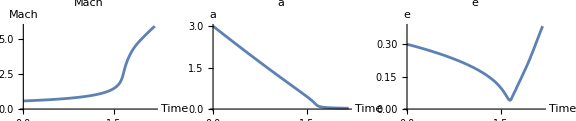

```mathematica
data=Evolve[1,0.3,3.0,0.5,0.5];

GraphicsRow[{ListLinePlot[Transpose[{data["Time"],data["Mach"]}],PlotLabel->"Mach",AxesLabel->{"Time","Mach"}],ListLinePlot[Transpose[{data["Time"],data["a"]}],PlotLabel->"a",AxesLabel->{"Time","a"}],ListLinePlot[Transpose[{data["Time"],data["e"]}],PlotLabel->"e",AxesLabel->{"Time","e"}]},ImageSize->Large,Spacings->1]
```

<|Time→{0.,0.112906,0.218981,0.318623,0.412206,0.500083,0.582589,0.660039,0.732729,0.800937,0.864928,0.924946,0.981225,1.03398,1.08342,1.12973,1.17308,1.21365,1.2516,1.28706,1.32017,1.35105,1.37983,1.40661,1.43149,1.45456,1.47593,1.49566,1.51385,1.53056,1.54588,1.55987,1.5726,1.58416,1.59462,1.60408,1.61262,1.62035,1.62737,1.63381,1.63977,1.64539,1.65077,1.65606,1.66138,1.66687,1.6727,1.679,1.68594,1.69363,1.70216,1.71162,1.72207,1.73364,1.74654,1.76101,1.77725,1.79562,1.8159,1.83794,1.86175,1.88765,1.91618,1.94653,1.97761,2.0105,2.04584,2.08409,2.12655,2.17392},Mach→{0.57735,0.597614,0.61859,0.640301,0.662775,0.686037,0.710116,0.735039,0.760838,0.787542,0.815184,0.843795,0.873411,0.904066,0.935798,0.968643,1.00264,1.03783,1.07426,1.11196,1.15099,1.19139,1.2332,1.27649,1.32129,1.36766,1.41567,1.46536,1.51679,1.57002,1.62513,1.68217,1.74121,1.80232,1.86558,1.93106,1.99884,2.06899,2.14161,2.21678,2.29458,2.37512,2.45848,2.54477,2.63409,2.72654,2.82224,2.92129,3.02383,3.12996,3.23981,3.35353,3.47123,3.59306,3.71917,3.84945,3.98356,4.12331,4.2651,4.40507,4.54227,4.67826,4.81481,4.95176,5.0905,5.23472,5.38643,5.54733,5.72037,5.91042},a→{3.,2.8,2.61333,2.43911,2.2765,2.12474,1.98309,1.85088,1.72749,1.61232,1.50484,1.40451,1.31088,1.22349,1.14192,1.06579,0.99474,0.928424,0.866529,0.808761,0.754843,0.70452,0.657552,0.613716,0.572801,0.534614,0.498973,0.465709,0.434661,0.405684,0.378638,0.353396,0.329836,0.307847,0.287324,0.268169,0.250291,0.233605,0.218031,0.203496,0.189929,0.177267,0.16545,0.15442,0.144125,0.134517,0.125549,0.117179,0.109367,0.102076,0.0952709,0.0889195,0.0829915,0.0774587,0.0722948,0.0674844,0.063017,0.0588178,0.054972,0.0515341,0.0484679,0.0456911,0.0431362,0.0407832,0.0385904,0.0364933,0.0344666,0.0324962,0.0305599,0.0286262},e→{0.3,0.291315,0.282761,0.274337,0.266041,0.25787,0.249822,0.241893,0.23408,0.226378,0.218784,0.211292,0.203897,0.196594,0.189378,0.182242,0.175181,0.168188,0.161257,0.154383,0.147559,0.140781,0.134043,0.127343,0.120681,0.114059,0.107485,0.100972,0.0945426,0.0882278,0.0820701,0.0761225,0.070447,0.065111,0.0601822,0.055723,0.0517856,0.0484094,0.0456214,0.0434395,0.0418779,0.0409536,0.0406925,0.0411343,0.0423329,0.044349,0.0472287,0.0509634,0.0554418,0.0604391,0.0657098,0.0711794,0.0770806,0.0838547,0.0918453,0.10103,0.111133,0.122246,0.134471,0.147918,0.16271,0.17898,0.196879,0.216566,0.238223,0.262045,0.28825,0.317075,0.348782,0.383661}|>

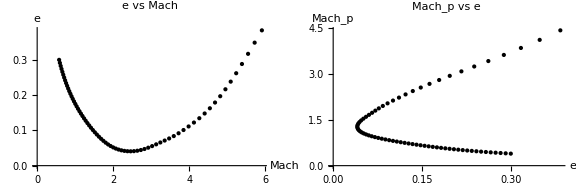

```mathematica
data

GraphicsRow[{ListPlot[Transpose[{data["Mach"],data["e"]}],PlotLabel->"e vs Mach",AxesLabel->{"Mach","e"},PlotStyle->{Black,PointSize[Small]}],
ListPlot[Transpose[{data["e"],data["Mach"]*Sqrt[(1+data["e"])/(1-data["e"])]/2}],PlotLabel->"Mach_p vs e",AxesLabel->{"e","Mach_p"},PlotStyle->{Black,PointSize[Small]}]},ImageSize->Large,Spacings->1]

(*e0 = 0.3; a0 = 3; q1 =0.5; q2 = 0.5;
filename=StringReplace[StringTemplate["evolution_e``_a``_q1``_q2``.csv"][e0,a0,q1,q2],"."->"_"];
Export[filename,Prepend[Transpose[{data["Time"],data["Mach"],data["a"],data["e"]}],{"Time","Mach","a","e"}],"CSV"]*)
```

```mathematica
MdotEdotVector[q1_,q2_][Mach_,e_]:=Module[{Ω,E,L,μ,a,adot,edot,Ωdot,Mdot,edotval,ldotval},
μ=q1 q2 M;
a=M G(1/cs/Mach)^2;
Ω=Sqrt[M G /a^3];
E=-M G  μ/(2 a);
L=μ Sqrt[G M   a (1-e^2)];
{edotval,ldotval}=EdotLdot[M,Mach,e,a,Ω,q1,q2];
adot=-a/E*edotval;
edot=-((1-e^2)/e)*(edotval/(2 E)+ldotval/L);
Ωdot=-3/2/a*Ω*adot;
Mdot=Ωdot a/cs+adot Ω/cs;
{Mdot,edot}]
MpdotEdotVector[q1_,q2_][Machp_,e_]:=Module[{Ω,E,L,μ,a,adot,edot,Ωdot,Mdot,edotval,ldotval, Mpdot, Mach},
Mach= Machp * Sqrt[(1-e)/(1+e)]*(1+q2/q1)/(q2/q1); (* q2/q1 means we are looking at the m1*)
μ=q1 q2 M;
a=M G(1/cs/Mach)^2;
Ω=Sqrt[M G /a^3];
E=-M G  μ/(2 a);
L=μ Sqrt[G M   a (1-e^2)];
{edotval,ldotval}=EdotLdot[M,Mach,e,a,Ω,q1,q2];
adot=-a/E*edotval;
edot=-((1-e^2)/e)*(edotval/(2 E)+ldotval/L);
Ωdot=-3/2/a*Ω*adot;
Mdot=Ωdot a/cs+adot Ω/cs;
Mpdot = q2/q1/(1+q2/q1)*( Sqrt[(1+e)/(1-e)])*Mdot+(Mach)*(1/Sqrt[(1+e)*(1-e)^3])*edot;
{Mpdot,edot}]
```

```mathematica
(*Choose parameters*)
q1=0.5;q2=0.5;
mdotEdot=MdotEdotVector[q1,q2];

(*Generate vector field grid*)
grid=Flatten[Table[{Mach,e,Sequence@@mdotEdot[Mach,e]},{Mach,0.2,7.0,0.4},{e,0.05,0.95,0.05}],1];
```

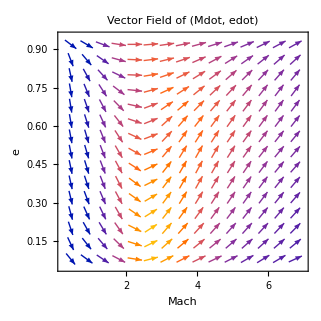

```mathematica
ListVectorPlot[({#1[[;;2]],#1[[3;;]]}&)/@grid,VectorScale->{Small,Scaled[0.05],None},VectorStyle->Arrowheads[0.02],FrameLabel->{"Mach","e"},Axes->False,Frame->True,PlotLabel->"Vector Field of (Mdot, edot)",ImageSize->Large]
```

```mathematica
(*Convert floats to strings with no dots,e.g.0.3->03*)sanitize[x_]:=StringReplace[ToString[NumberForm[x,{3,2}]],"."->""]

q1str=sanitize[q1];
q2str=sanitize[q2];
MachMin=0.2;MachMax=7.0;
eMin=0.05;eMax=0.95;

machstr=sanitize[MachMin]<>"to"<>sanitize[MachMax];
estr=sanitize[eMin]<>"to"<>sanitize[eMax];

filename=StringTemplate["vectorfield_q1``_q2``_mach``_e``.csv"][q1str,q2str,machstr,estr];

Export[filename,Prepend[grid,{"Mach","e","Mdot","edot"}],"CSV"]
```

vectorfield_q1050_q2050_mach020to700_e005to095.csv

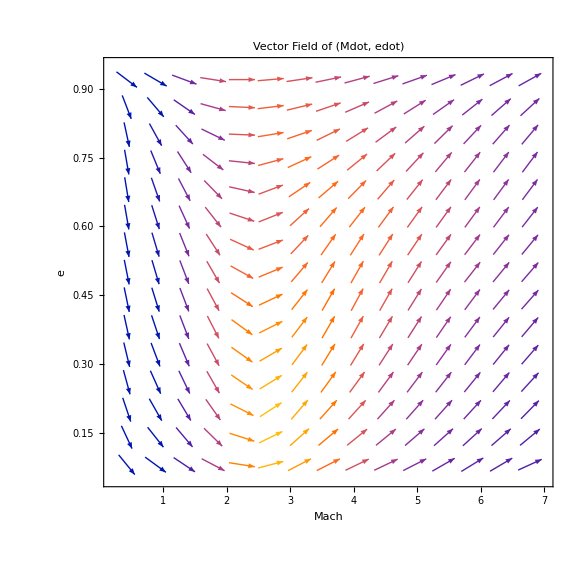

```mathematica
(*Load data*)data=Rest@Import[filename,"CSV"];

(*Convert each row:{Mach,e,Mdot,edot}->{{Mach,e},{Mdot,edot}}*)
vfData={{#[[1]],#[[2]]},{#[[3]],#[[4]]}}&/@data;

(*Plot full vector field*)
ListVectorPlot[vfData,VectorScale->{Small,Scaled[0.05],None},VectorStyle->Arrowheads[0.02],FrameLabel->{"Mach","e"},Frame->True,Axes->False,PlotLabel->"Vector Field of (Mdot, edot)",ImageSize->Large]
```

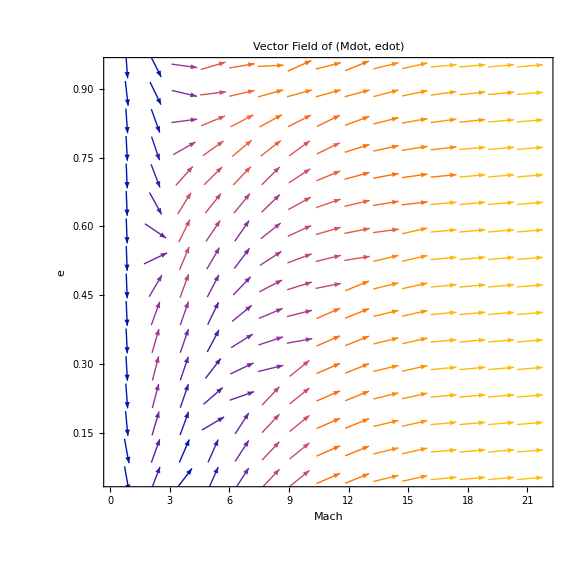

```mathematica
transformedData=grid/. {mach_,e_,mdot_,edot_}:>Module[{Mp=mach/2 Sqrt[(1+e)/(1-e)],dMp},(*Chain rule for dMp*)dMp=(1/2 Sqrt[(1+e)/(1-e)])*mdot+(mach/2)*(1/Sqrt[(1+e)*(1-e)^3])*edot;
{Mp,e,dMp,edot}];


(*Plot*)
ListVectorPlot[({#1[[;;2]],#1[[3;;]]}&)/@transformedData,VectorScale->{Small,Scaled[0.05],None},VectorStyle->Arrowheads[0.02],FrameLabel->{"Mach","e"},Axes->False,Frame->True,PlotLabel->"Vector Field of (Mdot, edot)",ImageSize->Large]
```

GridData1whole.csv

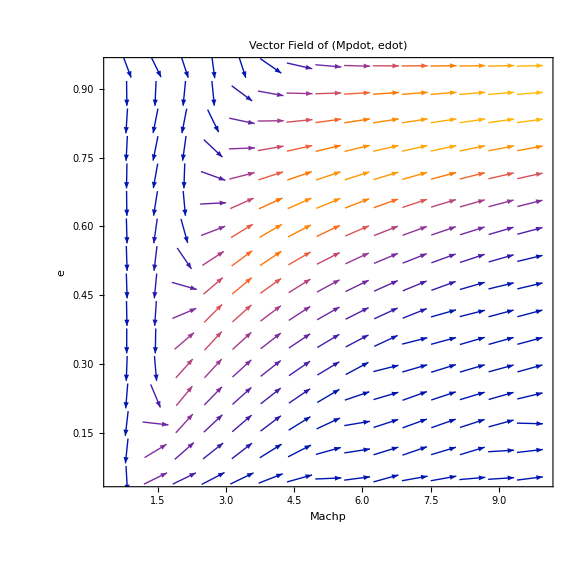

```mathematica
q1=0.5;q2=0.5;
mpdotEdot=MpdotEdotVector[q1,q2];
MachMin=0.5;MachMax=10.0;
eMin=0.05;eMax=0.95;

grid=Flatten[Table[{Machp,e,Sequence@@mpdotEdot[Machp,e]},{Machp,MachMin,MachMax,0.5},{e,eMin,eMax,0.05}],1];
(*q1str=sanitize[q1];
q2str=sanitize[q2];
machstr=sanitize[MachMin]<>"to"<>sanitize[MachMax];
estr=sanitize[eMin]<>"to"<>sanitize[eMax];*)

(*filename=StringTemplate["mpfield_q1``_q2``_mach``_e``.csv"][q1str,q2str,machstr,estr];

Export[filename,Prepend[grid,{"Machp","e","Mpdot","edot"}],"CSV"]*)
Export["GridData1whole.csv",Prepend[grid,{"Machp","e","Mpdot","edot"}],"CSV"]
ListVectorPlot[({#1[[;;2]],#1[[3;;]]}&)/@grid,VectorScale->{Small,Scaled[0.05],None},VectorStyle->Arrowheads[0.02],FrameLabel->{"Machp","e"},Axes->False,Frame->True,PlotLabel->"Vector Field of (Mpdot, edot)",ImageSize->Large]
```

```mathematica
Export["GridData1.csv",Prepend[grid,{"Machp","e","Mpdot","edot"}],"CSV"]
```

GridData1.csv

```mathematica
(*grid={{Mp,e,Mpdot,edot},...}*)(*Place at (e,Mp) and swap components to (edot,Mpdot)*)scale=0.02;  (*shrink factor for the whole arrow length*)
vecsSwappedSmall=({{#[[2]],#[[1]]},scale*{#[[4]],#[[3]]}}&)/@grid;

(*Background amplitude at (e,Mp)*)
magDataSwapped=({#[[2]],#[[1]],Sqrt[#[[3]]^2+#[[4]]^2]}&)/@grid;
ex=magDataSwapped[[All,1]];
mpy=magDataSwapped[[All,2]];
xrange={Min[ex],Max[ex]};
yrange={Min[mpy],Max[mpy]};
```

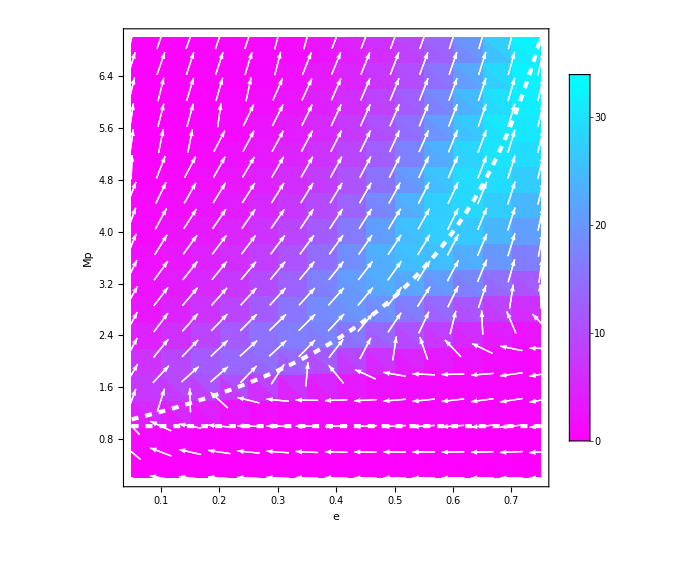

```mathematica
Show[ListDensityPlot[magDataSwapped,ColorFunction->(RGBColor[1-#,#,1]&),ColorFunctionScaling->True,InterpolationOrder->2,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"e","Mp"},PlotLegends->Automatic,ImageSize->Large,Background->None (*Ensures the background uses the color function*)],ListVectorPlot[vecsSwappedSmall,VectorColorFunction->None,(*Prevents arrows from taking density plot colors*)VectorStyle->Directive[White,AbsoluteThickness[1]],(*White,thick arrows*)VectorScale->None,(*use your pre-scaled lengths*)VectorMarkers->{"Arrow",Scaled[0.000003]},(* <-HEAD SIZE HERE*)VectorStyle->Directive[White,AbsoluteThickness[0.8]],(*Use pre-scaled vectors*)VectorPoints->All,Frame->True,Axes->False],(*Dashed white horizontal line:Mp=1*)Graphics[{Directive[White,Dashed,AbsoluteThickness[3]],Line[{{xrange[[1]],1},{xrange[[2]],1}}]}],(*Dashed white curve:Mp=(1+e)/(1-e) over the visible e-range*)Plot[(1+e)/(1-e),{e,xrange[[1]],xrange[[2]]},PlotStyle->Directive[White,Dashed,AbsoluteThickness[3]],PlotRange->{xrange,yrange}]]
```

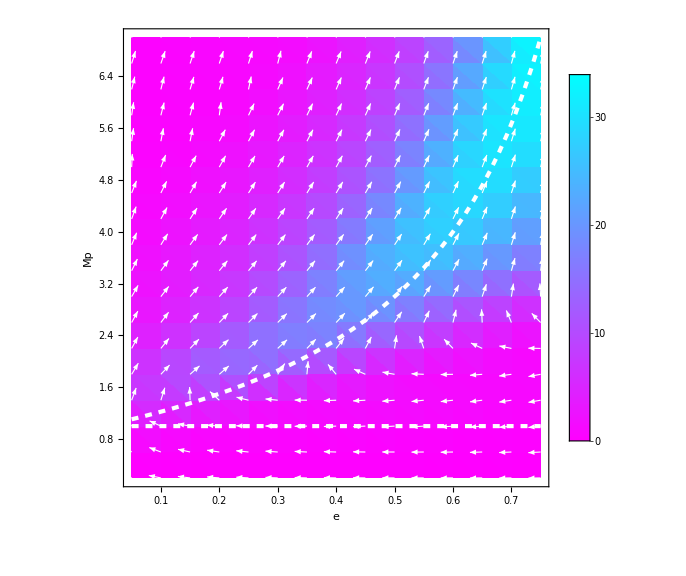

```mathematica
(*Ranges for aspect correction*)dx=xrange[[2]]-xrange[[1]];
dy=yrange[[2]]-yrange[[1]];

constLen=0.03*dx;   (*choose a fixed length in "e" units;tweak 0.03*)
ah=0.008;           (*arrowhead size (fraction of arrow length)*)
shaft=0.8;          (*shaft thickness*)

(*vecsSwappedSmall:{{{e,Mp},{edot,Mpdot}},...}*)
arrowPrims=Map[Function[{pv},Module[{p=pv[[1]],v=pv[[2]],vScreen,n,uScreen,uData},(*normalize in screen space so arrows look same length*)vScreen={v[[1]],v[[2]]*(dx/dy)};
n=Norm[vScreen];
If[n==0,{White,PointSize[0.004],Point[p]},(*draw a dot for zero vector*)uScreen=vScreen/n;(*unit vector on screen*)(*convert unit back to data coords*)uData={uScreen[[1]],uScreen[[2]]*(dy/dx)};
{White,AbsoluteThickness[shaft],Arrowheads[ah],Arrow[{p,p+constLen*uData}]}]]],vecsSwappedSmall];

arrowLayer=Graphics[arrowPrims,PlotRange->{xrange,yrange},Background->None];



Show[ListDensityPlot[magDataSwapped,ColorFunction->(RGBColor[1-#,#,1]&),ColorFunctionScaling->True,InterpolationOrder->2,PlotRange->{xrange,yrange},Frame->True,Axes->False,FrameLabel->{"e","Mp"},PlotLegends->Automatic,ImageSize->Large,Background->None],arrowLayer,Graphics[{Directive[White,Dashed,AbsoluteThickness[3]],Line[{{xrange[[1]],1},{xrange[[2]],1}}]}],Plot[(1+e)/(1-e),{e,xrange[[1]],xrange[[2]]},PlotStyle->Directive[White,Dashed,AbsoluteThickness[3]],PlotRange->{xrange,yrange}]]
```